## Basic setup

The first 1000 primes with modulo 2^pedges can be assembled like so:

```mathematica
primesGraph[p_Integer:2, amount_Integer:1000]:=
Module[
{primes, accept,mapping,targets,adjMap},
primes = Array[Prime,amount];
accept = IntegerQ[Log[p,Abs[#1-#2]]]&;
mapping=Function[{u},Select[primes,accept[u,#]&]];
targets = mapping/@primes;
adjMap = Flatten[Apply[Function[{u},#1->u]/@#2&,Transpose[{primes,targets}],1]];
UndirectedGraph[adjMap] (*returns an undirected graph*)
]
```

The standard base-2 graph looks like the following:

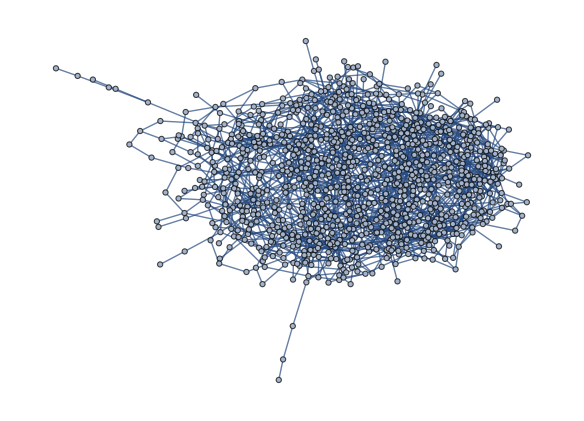

```mathematica
g2 = primesGraph[]
```

```mathematica
(*Export["/Users/swa/Desktop/primes-graph/g-2-1000.graphml",g];*)
```

The base-n graphs for n=3,4,5,6,7,8

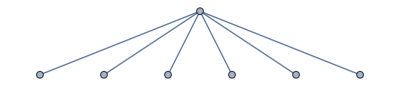
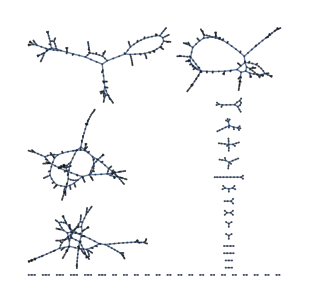

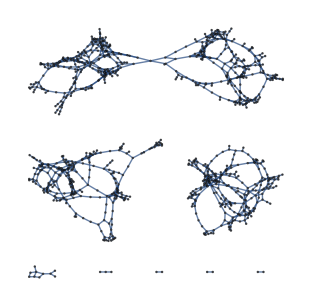

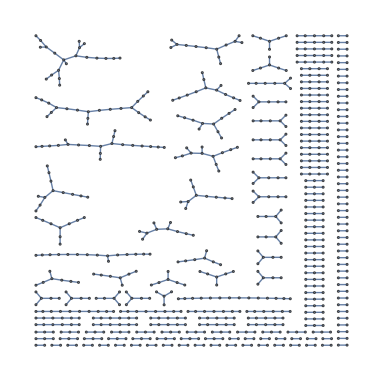

```mathematica
Table[primesGraph[n],{n,3,8}]
```

```mathematica
GraphDiameter[g2]
```

14